```mathematica
Integrate[t^k(1-t)^(n-k),{t,1/2,1}]
```

ConditionalExpression[-Beta[1/2,1+k,1-k+n]+(Gamma[1+k] Gamma[1-k+n])/Gamma[2+n],Re[k-n]<1]

```mathematica
Gamma[2+n]/(Gamma[1+k] Gamma[1+n-k])(-Beta[1/2,1+k,1+n-k]+(Gamma[1+k] Gamma[1+n-k])/Gamma[2+n])//FullSimplify
```

1-(Beta[1/2,1+k,1-k+n] Gamma[2+n])/(Gamma[1+k] Gamma[1-k+n])

```mathematica
f[k_,n_]:=1-(Beta[1/2,1+k,1-k+n] Gamma[2+n])/(Gamma[1+k] Gamma[1-k+n])
```

```mathematica
f[22,39]//N
```

0.785205

```mathematica
f[12,12+11]//N
```

0.58059

```mathematica
f[20,30]//N
```

0.964622

```mathematica
Manipulate[Plot[f[k,n],{k,0,n}],{n,10,100,1}]
```

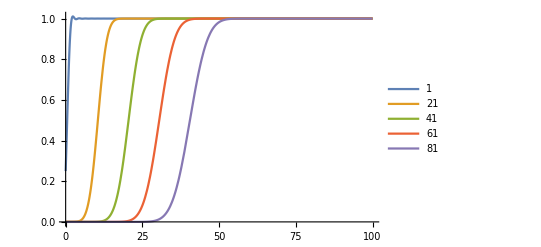

```mathematica
steps=Table[f[k,n],{n,1,100,20}];
Plot[steps,{k,0,100},PlotLegends->Range[1,100,20]]
```

```mathematica
Limit[f[n/2+1,n],n->∞]
```

Limit[1-(Beta[1/2,2+n/2,n/2] Gamma[2+n])/(Gamma[2+n/2] Gamma[n/2]),n→∞]

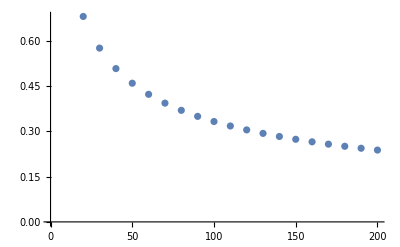

```mathematica
f[n_]:=FindFit[Table[f[k,n],{k,0,n}],1/(1+ⅇ^(-a(x-n/2))),{a},x];
ListPlot@Table[{n,f[n]⟦1,2⟧},{n,20,200,10}]
```

```mathematica
data=Table[{n,f[n]⟦1,2⟧},{n,30,3000,100}]//OutputForm
```

{{30, 0.574972}, {130, 0.292866}, {230, 0.221956}, {330, 0.185892}, {430, 0.163128}, {530, 0.147092}, {630, 0.135012}, {730, 0.125491}, 
 
  {830, 0.117736}, {930, 0.111262}, {1030, 0.10575}, {1130, 0.100983}, {1230, 0.0968085}, {1330, 0.0931119}, {1430, 0.0898088}, {1530, 0.086834}, 
 
  {1630, 0.0841365}, {1730, 0.0816757}, {1830, 0.079419}, {1930, 0.0773395}, {2030, 0.0754152}, {2130, 0.0736278}, {2230, 0.0719617}, 
 
  {2330, 0.0704039}, {2430, 0.068943}, {2530, 0.0675695}, {2630, 0.0662749}, {2730, 0.0650519}, {2830, 0.0638943}, {2930, 0.0627964}}

```mathematica
Show[ListPlot[data,PlotStyle->Gray],Plot[fit[x],{x,30,3000},PlotStyle->Red]]
```

ListPlot::lpn: {{30., 0.574972}, {130., 0.292866}, {230., 0.221956}, {330., 0.185892}, {430., 0.163128}, {530., 0.147092}, {630., 0.135012}, {730., 0.125491}, {830., 0.117736}, {930., 0.111262}, {1030., 0.10575}, {1130., 0.100983}, {1230., 0.0968085}, {1330., 0.0931119}, {1430., 0.0898088}, {1530., 0.086834}, {1630., 0.0841365}, {1730., 0.0816757}, {1830., 0.079419}, {<<2>>}, {<<2>>}, {2130., 0.0736278}, {2230., 0.0719617}, {2330., 0.0704039}, {2430., 0.068943}, {2530., 0.0675695}, {2630., 0.0662749}, {2730., 0.0650519}, {2830., 0.0638943}, {2930., 0.0627964}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ListPlot[FrameBox[« 543 », Rule[BoxFrame, False], Rule[BoxMargins, False]], PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.5`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.33333333333333337`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

Show[ListPlot[{{30, 0.574972}, {130, 0.292866}, {230, 0.221956}, {330, 0.185892}, {430, 0.163128}, {530, 0.147092}, {630, 0.135012}, {730, 0.125491}, {830, 0.117736}, {930, 0.111262}, {1030, 0.10575}, {1130, 0.100983}, {1230, 0.0968085}, {1330, 0.0931119}, {1430, 0.0898088}, {1530, 0.086834}, {1630, 0.0841365}, {1730, 0.0816757}, {1830, 0.079419}, {1930, 0.0773395}, {2030, 0.0754152}, {2130, 0.0736278}, {2230, 0.0719617}, {2330, 0.0704039}, {2430, 0.068943}, {2530, 0.0675695}, {2630, 0.0662749}, {2730, 0.0650519}, {2830, 0.0638943}, {2930, 0.0627964}},PlotStyle→GrayLevel[0.5]],-Graphics-]

```mathematica
Manipulate[Show[ListPlot[Table[{k,f[k,n]},{k,0,n,2}],PlotStyle->Red],Plot[1/(1+ⅇ^(-3 n^(-.48)(x-n/2))),{x,0,n}]],{n,10,100,1}]
```